## Polyhedra

```mathematica
If[$VersionNumber<8,
<<"Combinatorica`";
UndirectedEdge=List;
IsomorphicGraphQ=Combinatorica`IsomorphicQ;
]
```

```mathematica
ToGraph[z_]:=If[$VersionNumber<8,FromUnorderedPairs,Graph][UndirectedEdge@@#&/@(List@@Position[z,#]⟦All,1⟧&/@Union[Cases[z,_Integer,∞]])]
```

### The polyhedra database

```mathematica
PolyhedraNames={};
```

```mathematica
SavePolyhedraNames[]:=Put[PolyhedraNames,FileNameJoin[{NotebookDirectory[],"polyhedra.m"}]];
LoadPolyhedraNames[]:=(PolyhedraNames=Get[FileNameJoin[{NotebookDirectory[],"polyhedra.m"}]];)
```

```mathematica
NamePolyhedron[G_]:=Module[{r=ToGraph[G],name},
name=Unique["p"];
AppendTo[PolyhedraNames,name->G];
Print["Naming a new polyhedron: ",name->showGraph[r], " ",G];
name
]
```

```mathematica
IdentifyPolyhedron[G_]:=Module[{found,name},
found=Cases[PolyhedraNames,(name_->H_/;IsomorphicGraphQ[ToGraph[H],ToGraph[G]]):>name];
If[Length[found]>1,
Print["Warning! PolyhedraNames contains isomorphs."];Abort[],
If[Length[found]==0,
name=NamePolyhedron[G],
found⟦1⟧
]
]
]
```

```mathematica
IdentifyPolyhedron[d^(k_.)z_.]:=d^k IdentifyPolyhedron[z]
IdentifyPolyhedron[b^(k_.)z_.]:=b^k IdentifyPolyhedron[z]
IdentifyPolyhedron[t^(k_.)z_.]:=t^k IdentifyPolyhedron[z]
IdentifyPolyhedron[Q^(k_.)z_.]:=Q^k IdentifyPolyhedron[z]
IdentifyPolyhedron[n_Integer]:=n
```

```mathematica
IdentifyPolyhedra[X_]:=Module[{constant,arrays,Ys},
Ys=Union[Cases[X,_Y|_P,∞]];
If[Ys==={},X,
arrays=CoefficientArrays[X,Ys];
constant=arrays⟦1⟧;
arrays=Rest[arrays];
Together[constant+Plus@@Cases[Flatten[ArrayRules/@arrays],(i:{__Integer}->c_):>IdentifyPolyhedron[Times@@Ys⟦i⟧]c]]
]
]
```

```mathematica
If[$VersionNumber<8,
showGraph=GraphPlot[#,Method->"SpringEmbedding"]&,
showGraph=#&
];
```

```mathematica
DisplayPolyhedraNames[]:=#⟦1⟧->showGraph[ToGraph[#⟦2⟧]]&/@PolyhedraNames
```

### Polyhedra identities

```mathematica
SkeinContexts={"SO(3)","Deligne","Vogel","G2","H3",{1,0,1,1,3},{1,0,1,1,4},{1,0,1,1,5},{1,0,1,1,6}};
```

```mathematica
(SkeinContextParents={"SO(3)"->{{1,0,1,1,3}},{1,0,1,1,3}->{{1,0,1,1,4}},{1,0,1,1,4}->{{1,0,1,1,5}},{1,0,1,1,5}->{{1,0,1,1,6}},"Vogel"->{{1,0,1,1,6}},"Deligne"->{{1,0,1,1,5},"Vogel"},"G2"->{{1,0,1,1,4}},"H3"->{{1,0,1,1,4}}})//TableForm
```

SO(3)→{{1,0,1,1,3}}
{1,0,1,1,3}→{{1,0,1,1,4}}
{1,0,1,1,4}→{{1,0,1,1,5}}
{1,0,1,1,5}→{{1,0,1,1,6}}
Vogel→{{1,0,1,1,6}}
Deligne→{{1,0,1,1,5},Vogel}
G2→{{1,0,1,1,4}}
H3→{{1,0,1,1,4}}

```mathematica
VariableSubstitutions[content_]:={}
```

```mathematica
VariableSubstitutions["Deligne"]={Q->z^3,t->XXX};
```

```mathematica
Clear[DiagramReductions]
DiagramReductions[context_]:={}
```

```mathematica
Clear[PolyhedraEvaluationRules]
PolyhedraEvaluationRules[context_]:={}
```

## Evaluating diagrams

### Tiny faces

We always immediately remove loops, monogons, bigons and triangles.

```mathematica
Do[
Y/:RotateLeft[Y[a_,bb_,c_],i]RotateLeft[Y[c_,bb_,d_],j]:=b P[a,d]
,{i,0,2},{j,0,2}]
```

```mathematica
Y[a_,a_,b_]:=0
Y[a_,b_,a_]:=0
Y[b_,a_,a_]:=0
```

```mathematica
SetAttributes[P,Orderless]
```

```mathematica
P[a_,a_]:=d
P/:P[a_,b_]^2:=d
P/:P[a_,b_]P[b_,c_]:=P[a,c]
```

```mathematica
Do[
P/:RotateLeft[Y[a_,b_,c_],i]P[a_,d_]:=Y[b,c,d]
,{i,0,2}]
```

```mathematica
Do[
Y/:RotateLeft[Y[a_,b_,c_],i]RotateLeft[Y[b_,d_,e_],j]RotateLeft[Y[c_,e_,f_],k]:=t Y[a,d,f]
,{i,0,2},{j,0,2},{k,0,2}]
```

## Diagram properties

```mathematica
Unprotect[ConnectedComponents];
Diagram/:ConnectedComponents[Diagram[_,contents_]]:=Length[timesToList[contents/.Y->Yg//.glomRule]]
```

```mathematica
glomRule={Yg[A___,b_,C___]Yg[D___,b_,E___]:>Union[Yg[A,C,D,E,b]]};
```

```mathematica
NumberOfVertices[Diagram[_,contents_]]:=Count[contents,_Y]
```

```mathematica
NumberOfInternalFaces[d:Diagram[boundary_,contents_]]:=NumberOfInternalFaces[d]=1/2 NumberOfVertices[d]+ConnectedComponents[d]-1/2 Length[boundary]
```

## Enumerating diagrams

### Canonical labelling and isomorphism

```mathematica
timesToList[X_Times]:=List@@X
timesToList[X_]:={X}
```

```mathematica
canonicalLabellingCounter=0;
```

```mathematica
K0=10000000;
```

```mathematica
Clear[canonicalLabelling]
canonicalLabelling[d:Diagram[boundary_,contents_]]:=canonicalLabelling[d]=Module[{limit=∞,m0=K0,m,newBoundary,Yrule,c,t,r,sortOrder},
canonicalLabellingCounter--;
sortOrder[2]=0;
sortOrder[1]=1;
sortOrder[_]=2;
m:=(m0++);
newBoundary=Table[m,{Length[boundary]}];
boundaryReplacements=Thread[boundary->newBoundary];
c=contents/.boundaryReplacements;
Yrule=y_Y:>Sort[{y,RotateLeft[y],RotateRight[y]}]⟦1⟧;
c=c/.Yrule;
While[c=!=0∧limit-->0∧!FreeQ[c,n_Integer/;n<K0],
t=SortBy[Cases[timesToList[c],_Y],With[{ns=Sort[Cases[(List@@#),n_/;n≥K0]]},{sortOrder[Length[ns]],ns}]&]⟦1⟧;
r=If[Count[List@@t,n_/;n<K0]==1,
Cases[List@@t,n_/;n<K0]⟦1⟧->m,
t⟦Mod[Position[List@@t,n_/;n≥K0]⟦1,1⟧,3]+1⟧->m
];
c=c/.r;
c=c/.Yrule;
];
Diagram[newBoundary,c]
]
canonicalLabelling[d:Diagram[{},_]]:=d
```

```mathematica
DiagramsIsomorphicQ[d1_Diagram,d2_Diagram]:=canonicalLabelling[d1]===canonicalLabelling[d2]
```

### Generating diagrams

It would be nice to replace this with something based on plantri!

```mathematica
k0=10000;
freshLabel:=k0++
```

```mathematica
Clear[diagramsByVertexNumber]
```

```mathematica
diagramsByVertexNumber[0,0]:={Diagram[{},1]}
diagramsByVertexNumber[1,1]:={}
diagramsByVertexNumber[n_/;n<0,_]:={}
diagramsByVertexNumber[_,k_/;k<0]:={}
```

```mathematica
diagramsByVertexNumber[n_,k_]:=diagramsByVertexNumber[n,k]=isomorphismRepresentatives[addCups[diagramsByVertexNumber[n-2,k]]~Join~addForks[diagramsByVertexNumber[n-1,k-1]]~Join~addHs[diagramsByVertexNumber[n,k-2]]]
```

```mathematica
addCups[X_List]:=Flatten[addCups/@X]
addForks[X_List]:=Flatten[addForks/@X]
addHs[X_List]:=Flatten[addHs/@X]
```

```mathematica
addCups[Diagram[boundary_,contents_]]:=With[{k1=freshLabel,k2=freshLabel},Table[Diagram[RotateRight[RotateLeft[boundary,i]~Join~{k1,k2},i],contents P[k1,k2]],{i,0,Length[boundary]}]]
```

```mathematica
addForks[Diagram[boundary_,contents_]]:=
With[{k1=freshLabel,k2=freshLabel},
Table[Diagram[Take[boundary,i]~Join~{k1,k2}~Join~Drop[boundary,i+1],contents Y[boundary⟦i+1⟧,k1,k2]],{i,0,Length[boundary]-1}]~Join~{Diagram[{k2}~Join~Most[boundary]~Join~{k1},contents Y[boundary⟦-1⟧,k1,k2]],Diagram[{k1,k2}~Join~Most[boundary],contents Y[boundary⟦-1⟧,k1,k2]]}
]
```

```mathematica
addHs[dd:Diagram[boundary_,contents_]]:=addHs[dd]=
Module[{k1=freshLabel,k2=freshLabel,k3=freshLabel,aa,bb},
Cases[Table[
{aa,bb}={boundary⟦i+1⟧,boundary⟦Mod[i+1,Length[boundary]]+1⟧};
Diagram[RotateRight[{k1,k2}~Join~Drop[RotateLeft[boundary,i],2],i],contents Y[aa,k1,k3]Y[bb,k3,k2]],
{i,0,Length[boundary]-1}
],X_/;FreeQ[X,b|d|t]
]
]
```

```mathematica
isomorphismRepresentatives[X_List]:=isomorphismRepresentatives[{},X]
isomorphismRepresentatives[X_List,{}]:=X
isomorphismRepresentatives[{},{A_,B___}]:=isomorphismRepresentatives[{A},{B}]
isomorphismRepresentatives[X_List,{A_,B___}]:=If[MemberQ[DiagramsIsomorphicQ[#,A]&/@X,True],isomorphismRepresentatives[X,{B}],isomorphismRepresentatives[Append[X,A],{B}]]
```

```mathematica
Clear[Diagrams]
Diagrams[n_,k_]:=Diagrams[n,k]=Cases[Join@@Table[canonicalLabelling/@diagramsByVertexNumber[n,m],{m,Mod[n,2],n+2k-2,2}],d_/;NumberOfInternalFaces[d]==k]
```

```mathematica
Diagrams[n_,_≤k_]:=Join@@Table[Diagrams[n,i],{i,0,k}]
```

### Locating faces

```mathematica
PartialFace/:PartialFace[A___,b_,c_]PartialFace[b_,c_,D___]:=PartialFace[A,b,c,D]
```

```mathematica
PartialFace[A___,{b_,i_},C___]:=PartialFace[A,b,C]
```

```mathematica
PartialFace[a_,b_,C___,a_,b_]:=Face[a,b,C]
```

```mathematica
Faces[diagram_]:=List@@((diagram//.Flatten[Table[RotateLeft[Y[a_,b_,c_],i]RotateLeft[Y[c_,d_,e_],j]:>PartialFace[a,c,e]PartialFace[d,c,b]Y[a,b,{c,1}]Y[{c,2},d,e],{i,0,2},{j,0,2}]])/._Y:>1)
```

```mathematica
Faces[Diagram[boundary_,content_]]:=Faces[content]
```

```mathematica
edgesIncidentToCycle[Ys_,cycle_]:=Table[With[{a=cycle⟦i⟧,b=cycle⟦Mod[i,Length[cycle]]+1⟧},(Cases[Ys,Y[a,b,c_]|Y[c_,a,b]|Y[b,c_,a]:>{c,1}]~Join~Cases[Ys,Y[b,a,c_]|Y[c_,b,a]|Y[a,c_,b]:>{c,-1}])⟦1⟧],{i,1,Length[cycle]}]
```

```mathematica
edgesLeftOfCycle[Ys_,cycle_]:=Cases[edgesIncidentToCycle[Ys,cycle],{x_,-1}:>x]
```

```mathematica
FindSquares[dd_Diagram]:=Cases[Faces[dd],Face[a_,b_,c_,d_]:>Module[{Ys},
Ys=Cases[dd⟦2⟧,y_Y/;Count[y,a|b|c|d]==2];
Diagram[edgesLeftOfCycle[Ys,{a,b,c,d}],Times@@Ys]
]]
```

```mathematica
FindAdjacentPolygons[n1_,n2_][dd_Diagram]:=
Module[{faces=Faces[dd],pairs,unpackPair,bdy},
pairs=Flatten[Table[{f1,f2},{f1,Cases[faces,f_Face/;Length[f]==n1]},{f2,Cases[faces,f_Face/;Length[f]==n2∧Length[Intersection[f,f1]]==1]}],1];
unpackPair[{Face[A___,b_,C___],Face[D___,b_,E___]}]:=Module[{Ys},
Ys=Cases[dd⟦2⟧,y_Y/;Count[y,A|C|D|E]==2];
If[Length[Ys]≠n1+n2-2,Print["FindAdjacentPolygons failed..."];Abort[]];
bdy=edgesLeftOfCycle[Ys,{A,E,D,C}];
(* where does the boundary go? the first edge coming out of the n2 polygon *)
If[Length[{A}]≥2,bdy=RotateLeft[bdy,Length[{A}]-1]];
If[Length[bdy]≠n1+n2-4,Print["FindAdjacentPolygons failed..."];Abort[]];
Diagram[bdy,Times@@Ys]
];
unpackPair/@pairs
]
```

```mathematica
FindAdjacentSquares=FindAdjacentPolygons[4,4];
FindPentasquares=FindAdjacentPolygons[4,5];
```

```mathematica
DiagramsWithoutAdjacentSquares[n_,k_]:=DiagramsWithoutAdjacentSquares[n,k]=Cases[Diagrams[n,k],d_/;Length[FindAdjacentSquares[d]]==0]
DiagramsWithoutSmallPairs[n_,k_]:=DiagramsWithoutSmallPairs[n,k]=Cases[DiagramsWithoutAdjacentSquares[n,k],d_/;Length[FindPentasquares[d]]==0]
```

```mathematica
DiagramsWithoutAdjacentSquares[n_,_≤k_]:=Join@@Table[DiagramsWithoutAdjacentSquares[n,i],{i,0,k}]
```

```mathematica
DiagramsWithoutSmallPairs[n_,_≤k_]:=Join@@Table[DiagramsWithoutSmallPairs[n,i],{i,0,k}]
```

## Inner products

```mathematica
InnerProduct[d1_Diagram,d2_Diagram]:=InnerProduct[d1,d2]=Module[{k=Length[d1⟦1⟧],max1=Max[Cases[d1,_Integer,∞]],min2=Min[Cases[d2,_Integer,∞]],δ},
δ=max1-min2+1;
IdentifyPolyhedron[Product[P[d1⟦1,i⟧,d2⟦1,k+1-i⟧+δ],{i,1,k}]d1⟦2⟧(d2⟦2⟧/.(c:(_Y|_P):>(c/.n_Integer:>n+δ)))]
]
```

```mathematica
InnerProducts[n_,k_]:=Outer[InnerProduct,Diagrams[n,_≤k],Diagrams[n,_≤k]]
```

```mathematica
InnerProductsWithoutAdjacentSquares[n_,k_]:=Outer[InnerProduct,DiagramsWithoutAdjacentSquares[n,_≤k],DiagramsWithoutAdjacentSquares[n,_≤k]]
```

```mathematica
InnerProductsWithoutSmallPairs[n_,k_]:=Outer[InnerProduct,DiagramsWithoutSmallPairs[n,_≤k],DiagramsWithoutSmallPairs[n,_≤k]]
```

## Testing

```mathematica
Length[Diagrams[5,2]]===15
```

True

```mathematica
Union[Count[#,_Face]&/@(Faces/@Diagrams[5,2])]==={2}
```

True

```mathematica
Length/@(FindSquares/@Diagrams[5,2])==={2,2,2,2,2,2,2,2,2,2,1,1,1,1,1}
```

True

```mathematica
Length/@(FindAdjacentSquares/@Diagrams[4,2])==={2,2}
```

```mathematica
Length/@(FindPentasquares/@Diagrams[4,2])==={0,0}
```

```mathematica
FindPentasquares/@Diagrams[5,2]
```

{{},{},{},{},{},{},{},{},{},{},{Diagram[{10000000,10000001,10000002,10000003,10000004},{Y[10000000,10000005,10000006],Y[10000001,10000007,10000005],Y[10000002,10000008,10000007],Y[10000003,10000009,10000010],Y[10000004,10000011,10000009],Y[10000006,10000012,10000011],Y[10000008,10000010,10000012]}]},{Diagram[{10000004,10000000,10000001,10000002,10000003},{Y[10000000,10000005,10000006],Y[10000001,10000007,10000005],Y[10000002,10000009,10000010],Y[10000003,10000011,10000009],Y[10000004,10000006,10000008],Y[10000007,10000010,10000012],Y[10000008,10000012,10000011]}]},{Diagram[{10000000,10000001,10000002,10000003,10000004},{Y[10000000,10000005,10000006],Y[10000001,10000008,10000009],Y[10000002,10000010,10000008],Y[10000003,10000011,10000010],Y[10000004,10000006,10000007],Y[10000005,10000009,10000012],Y[10000007,10000012,10000011]}]},{Diagram[{10000001,10000002,10000003,10000004,10000000},{Y[10000000,10000005,10000006],Y[10000001,10000007,10000005],Y[10000002,10000008,10000009],Y[10000003,10000010,10000008],Y[10000004,10000011,10000010],Y[10000006,10000012,10000011],Y[10000007,10000009,10000012]}]},{Diagram[{10000003,10000004,10000000,10000001,10000002},{Y[10000000,10000005,10000006],Y[10000001,10000009,10000010],Y[10000002,10000011,10000009],Y[10000003,10000007,10000008],Y[10000004,10000006,10000007],Y[10000005,10000010,10000012],Y[10000008,10000012,10000011]}]}}

```mathematica
Length[DiagramsWithoutSmallPairs[5,1]]===6
```

True

```mathematica
Length[DiagramsWithoutSmallPairs[5,2]]===0
```

True

```mathematica
Length[DiagramsWithoutSmallPairs[6,2]]===12
```

True

```mathematica
InnerProducts[4,2]//MatrixForm
```

(d^2 | d | 0 | b d | b^2 d | b^3 d | b d t^2
d | d^2 | b d | 0 | b^2 d | b d t^2 | b^3 d
0 | b d | b^2 d | b d t | b d t^2 | b d t^3 | Cube
b d | 0 | b d t | b^2 d | b d t^2 | Cube | b d t^3
b^2 d | b^2 d | b d t^2 | b d t^2 | Cube | Prism[5] | Prism[5]
b^3 d | b d t^2 | b d t^3 | Cube | Prism[5] | Prism[6] | p55554444
b d t^2 | b^3 d | Cube | b d t^3 | Prism[5] | p55554444 | Prism[6])

```mathematica
InnerProducts[5,1]//MatrixForm
```

(0 | b d | b d^2 | b d | 0 | 0 | b^2 d | 0 | b d t | b^2 d | 0 | b d t^2 | b^3 d | b^3 d | b d t^2 | b^2 d t
b d | b d^2 | b d | 0 | 0 | b d t | b^2 d | b^2 d | 0 | 0 | b d t^2 | b^3 d | b^3 d | b d t^2 | 0 | b^2 d t
b d^2 | b d | 0 | 0 | b d | 0 | 0 | b^2 d | b^2 d | b d t | b^3 d | b^3 d | b d t^2 | 0 | b d t^2 | b^2 d t
b d | 0 | 0 | b d | b d^2 | b^2 d | b d t | 0 | b^2 d | 0 | b^3 d | b d t^2 | 0 | b d t^2 | b^3 d | b^2 d t
0 | 0 | b d | b d^2 | b d | b^2 d | 0 | b d t | 0 | b^2 d | b d t^2 | 0 | b d t^2 | b^3 d | b^3 d | b^2 d t
0 | b d t | 0 | b^2 d | b^2 d | b^3 d | b^2 d t | b^2 d t | b d t^2 | b d t^2 | b^2 d t^2 | b d t^3 | b d t^3 | b^2 d t^2 | Cube | b d t^3
b^2 d | b^2 d | 0 | b d t | 0 | b^2 d t | b d t^2 | b^3 d | b d t^2 | b^2 d t | b^2 d t^2 | Cube | b^2 d t^2 | b d t^3 | b d t^3 | b d t^3
0 | b^2 d | b^2 d | 0 | b d t | b^2 d t | b^3 d | b d t^2 | b^2 d t | b d t^2 | b d t^3 | b^2 d t^2 | Cube | b^2 d t^2 | b d t^3 | b d t^3
b d t | 0 | b^2 d | b^2 d | 0 | b d t^2 | b d t^2 | b^2 d t | b^2 d t | b^3 d | b d t^3 | b d t^3 | b^2 d t^2 | Cube | b^2 d t^2 | b d t^3
b^2 d | 0 | b d t | 0 | b^2 d | b d t^2 | b^2 d t | b d t^2 | b^3 d | b^2 d t | Cube | b^2 d t^2 | b d t^3 | b d t^3 | b^2 d t^2 | b d t^3
0 | b d t^2 | b^3 d | b^3 d | b d t^2 | b^2 d t^2 | b^2 d t^2 | b d t^3 | b d t^3 | Cube | b d t^4 | b d t^4 | Prism[5] | b Cube | Prism[5] | Cube t
b d t^2 | b^3 d | b^3 d | b d t^2 | 0 | b d t^3 | Cube | b^2 d t^2 | b d t^3 | b^2 d t^2 | b d t^4 | Prism[5] | b Cube | Prism[5] | b d t^4 | Cube t
b^3 d | b^3 d | b d t^2 | 0 | b d t^2 | b d t^3 | b^2 d t^2 | Cube | b^2 d t^2 | b d t^3 | Prism[5] | b Cube | Prism[5] | b d t^4 | b d t^4 | Cube t
b^3 d | b d t^2 | 0 | b d t^2 | b^3 d | b^2 d t^2 | b d t^3 | b^2 d t^2 | Cube | b d t^3 | b Cube | Prism[5] | b d t^4 | b d t^4 | Prism[5] | Cube t
b d t^2 | 0 | b d t^2 | b^3 d | b^3 d | Cube | b d t^3 | b d t^3 | b^2 d t^2 | b^2 d t^2 | Prism[5] | b d t^4 | b d t^4 | Prism[5] | b Cube | Cube t
b^2 d t | b^2 d t | b^2 d t | b^2 d t | b^2 d t | b d t^3 | b d t^3 | b d t^3 | b d t^3 | b d t^3 | Cube t | Cube t | Cube t | Cube t | Cube t | Prism[5])

```mathematica
Length[DiagramsWithoutSmallPairs[5,_≤3]]
```

16

```mathematica
Length[DiagramsWithoutSmallPairs[6,1]]
```

34

```mathematica
Length[DiagramsWithoutSmallPairs[6,1]]
```

34

```mathematica
InnerProductsWithoutSmallPairs[6,1]//MatrixForm
```

(«1»)

```mathematica
Length[DiagramsWithoutSmallPairs[6,2]]
```

12

```mathematica
InnerProductsWithoutSmallPairs[6,2]//MatrixForm
```

(«1»)

```mathematica
Union[Cases[InnerProductsWithoutSmallPairs[6,2],_Symbol|_Prism,∞]]
```

{b,Cube,d,p444444666,p444445566,p4444455666,p444455556,p444555555,p55554444,pAAAA,pAAAB,pAAAC,pAAAD,pAAAE,pAAAF,pAAAG,pAAAH,pAAAI,t,Prism[5],Prism[6]}

## Discovering relations

```mathematica
AddPolyhedraEvaluations[context_][X_]:=(PolyhedraEvaluationRules[context]=Union[PolyhedraEvaluationRules[context],Cases[X,(name_->value_)/;MemberQ[PolyhedraNames⟦All,1⟧,name],∞]];)
```

```mathematica
Clear[AddDiagramReduction]
AddDiagramReduction[context_][X_]:=(DiagramReductions[context]=Union[DiagramReductions[context],{X}];)
```

```mathematica
labels[stuff_]:=Union[Flatten[Cases[stuff,Y[a_,b_,c_]:>{a,b,c},{0,∞}]~Join~Cases[stuff,P[a_,b_]:>{a,b},{0,∞}]]]
```

```mathematica
refreshInternalLabels[Diagram[b_,c_]]:=Module[{labels=labels[c],internalLabels,replacements},
internalLabels=Complement[labels,b];
replacements=#->freshLabel&/@internalLabels;
Diagram[b,c/.replacements]
]
```

```mathematica
ApplySquareRelation[relation_][D:Diagram[bdy_,contents_]]:=Table[
Module[{newBoundary=square⟦1⟧,replacement,diff},
replacement=Thread[Diagrams[4,0]⟦1,1⟧->newBoundary];
diff=Complement[timesToList[contents],timesToList[square⟦2⟧]];
If[Length[diff]≠Length[timesToList[contents]]-Length[timesToList[square⟦2⟧]],Print["uh oh"];Abort[]];
Sum[relation⟦k⟧Diagram[bdy,(Times@@diff)(refreshInternalLabels[Diagrams[4,0]⟦k⟧]⟦2⟧/.replacement)],{k,1,4}]],
{square,FindSquares[D]}
]
```

```mathematica
ApplyAdjacentSquaresRelation[relation_][D:Diagram[bdy_,contents_]]:=Table[
Module[{newBoundary=square⟦1⟧,replacement,diff},
replacement=Thread[Diagrams[4,_≤1]⟦1,1⟧->newBoundary];
diff=Complement[timesToList[contents],timesToList[square⟦2⟧]];
If[Length[diff]≠Length[timesToList[contents]]-Length[timesToList[square⟦2⟧]],Print["uh oh"];Print[diff];Print[timesToList[contents]];Print[timesToList[square⟦2⟧]];Abort[]];
Sum[relation⟦k⟧Diagram[bdy,(Times@@diff)(refreshInternalLabels[Diagrams[4,_≤1]⟦k⟧]⟦2⟧/.replacement)],{k,1,5}]
],
{square,FindAdjacentSquares[D]}
]
```

```mathematica
ApplySquareRelation[relation_][X_Times]:=ApplySquareRelation[relation][Diagram[{},X]]/.Diagram[{},Y_]:>IdentifyPolyhedra[Y]
```

```mathematica
ApplyAdjacentSquaresRelation[relation_][X_Times]:=ApplyAdjacentSquaresRelation[relation][Diagram[{},X]]/.Diagram[{},Y_]:>IdentifyPolyhedra[Y]
```

```mathematica
ApplyDiagramReductions[context_][X_]:=Flatten[Table[Together[dr[X]/.PolyhedraEvaluationRules[context]],{dr,DiagramReductions[context]}]]
```

### {1, 0, 1, 1, 2}

```mathematica
Factor[Det[Outer[InnerProduct,Take[Diagrams[4,0],3],Take[Diagrams[4,0],3]]]]
```

b^2 d^3 (-1-d+d^2)

### {1, 0, 1, 1, 3}

```mathematica
Factor[Det[InnerProducts[4,0]]]
```

b^2 d^4 (-2 b+b d+t-d t) (b d+t+d t)

### {1, 0, 1, 1, 4}

```mathematica
Factor[Det[InnerProducts[4,1]]]
```

-b^2 d^4 (-2 b+b d+t-d t) (2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4)

```mathematica
Solve[%==0,Cube]
```

{{Cube→(2 b d (b^4+b^3 t-2 b^2 t^2+t^4+d t^4))/(b d+t+d t)}}

```mathematica
AddPolyhedraEvaluations[{1,0,1,1,4}][%]
```

```mathematica
NullSpace[InnerProducts[4,1]/.PolyhedraEvaluationRules[{1,0,1,1,4}]]
```

{{-(b^3+b^2 t-b t^2)/(b d+t+d t),-(b^3+b^2 t-b t^2)/(b d+t+d t),-(-b^2+t^2+d t^2)/(b d+t+d t),-(-b^2+t^2+d t^2)/(b d+t+d t),1}}

```mathematica
squareRelation=-Most[%⟦1⟧]
```

{(b^3+b^2 t-b t^2)/(b d+t+d t),(b^3+b^2 t-b t^2)/(b d+t+d t),(-b^2+t^2+d t^2)/(b d+t+d t),(-b^2+t^2+d t^2)/(b d+t+d t)}

```mathematica
Together[ApplySquareRelation[squareRelation][Cube/.PolyhedraNames]-(Cube/.PolyhedraEvaluationRules[{1,0,1,1,4}])]
```

{0,0,0,0,0,0}

```mathematica
AddDiagramReduction[{1,0,1,1,4}][ApplySquareRelation[squareRelation]]
```

```mathematica
ApplyDiagramReductions[{1,0,1,1,4}][Prism[5]/.PolyhedraNames]
```

{(-2 b^7 d+b^7 d^2-b^6 d t+2 b^6 d^2 t+7 b^5 d t^2+3 b^5 d^2 t^2+2 b^4 d t^3+2 b^4 d^2 t^3-6 b^3 d t^4-7 b^3 d^2 t^4-b^2 d t^5+b^2 d^3 t^5+3 b d t^6+6 b d^2 t^6+3 b d^3 t^6)/(b d+t+d t)^2,(-2 b^7 d+b^7 d^2-b^6 d t+2 b^6 d^2 t+7 b^5 d t^2+3 b^5 d^2 t^2+2 b^4 d t^3+2 b^4 d^2 t^3-6 b^3 d t^4-7 b^3 d^2 t^4-b^2 d t^5+b^2 d^3 t^5+3 b d t^6+6 b d^2 t^6+3 b d^3 t^6)/(b d+t+d t)^2,(-2 b^7 d+b^7 d^2-b^6 d t+2 b^6 d^2 t+7 b^5 d t^2+3 b^5 d^2 t^2+2 b^4 d t^3+2 b^4 d^2 t^3-6 b^3 d t^4-7 b^3 d^2 t^4-b^2 d t^5+b^2 d^3 t^5+3 b d t^6+6 b d^2 t^6+3 b d^3 t^6)/(b d+t+d t)^2,(-2 b^7 d+b^7 d^2-b^6 d t+2 b^6 d^2 t+7 b^5 d t^2+3 b^5 d^2 t^2+2 b^4 d t^3+2 b^4 d^2 t^3-6 b^3 d t^4-7 b^3 d^2 t^4-b^2 d t^5+b^2 d^3 t^5+3 b d t^6+6 b d^2 t^6+3 b d^3 t^6)/(b d+t+d t)^2,(-2 b^7 d+b^7 d^2-b^6 d t+2 b^6 d^2 t+7 b^5 d t^2+3 b^5 d^2 t^2+2 b^4 d t^3+2 b^4 d^2 t^3-6 b^3 d t^4-7 b^3 d^2 t^4-b^2 d t^5+b^2 d^3 t^5+3 b d t^6+6 b d^2 t^6+3 b d^3 t^6)/(b d+t+d t)^2}

### {1, 0, 1, 1, 5}

```mathematica
innerProducts=Outer[InnerProduct,Take[Diagrams[4,_<=2],6],Take[Diagrams[4,_<=2],6]];
```

```mathematica
Factor[Det[innerProducts]]
```

-b^2 d^3 (-Cube^3+5 b^4 Cube^2 d-Cube^3 d+b^8 Cube d^2-4 b^4 Cube^2 d^2+Cube^3 d^2-b^12 d^3+b^8 Cube d^3-2 b^3 Cube^2 d t+2 b^7 Cube d^2 t-12 b^6 Cube d^2 t^2+2 b^2 Cube^2 d^2 t^2+5 b^10 d^3 t^2+b^6 Cube d^3 t^2-2 b Cube^2 d t^3+2 b^5 Cube d^2 t^3+2 b Cube^2 d^2 t^3-4 b^9 d^3 t^3-2 b^5 Cube d^3 t^3+3 Cube^2 d t^4-b^4 Cube d^2 t^4-8 b^8 d^3 t^4+11 b^4 Cube d^3 t^4-3 Cube^2 d^3 t^4-2 b^8 d^4 t^4+8 b^3 Cube d^2 t^5+6 b^7 d^3 t^5-8 b^3 Cube d^3 t^5+4 b^7 d^4 t^5-5 b^2 Cube d^2 t^6+16 b^6 d^3 t^6-4 b^2 Cube d^3 t^6-4 b^6 d^4 t^6+b^2 Cube d^4 t^6-2 b Cube d^2 t^7-16 b^5 d^3 t^7+2 b Cube d^4 t^7+b^4 d^3 t^8-2 b^4 d^4 t^8+2 b^3 d^3 t^9+4 b^3 d^4 t^9+b^2 d^3 t^10-b^2 d^5 t^10-4 b^3 Cube d Prism[5]+4 b^7 d^2 Prism[5]+2 b^3 Cube d^2 Prism[5]-2 b^7 d^3 Prism[5]+2 b^2 Cube d t Prism[5]+2 b^6 d^2 t Prism[5]-2 b^2 Cube d^2 t Prism[5]+4 b Cube d t^2 Prism[5]-2 b^5 d^2 t^2 Prism[5]+2 b Cube d^2 t^2 Prism[5]+2 b^5 d^3 t^2 Prism[5]-2 b Cube d^3 t^2 Prism[5]-2 Cube d t^3 Prism[5]+2 Cube d^3 t^3 Prism[5]-4 b^3 d^2 t^4 Prism[5]+2 b^3 d^3 t^4 Prism[5]+6 b^2 d^2 t^5 Prism[5]-2 b^2 d^4 t^5 Prism[5]-2 b d^2 t^6 Prism[5]+2 b d^4 t^6 Prism[5]-2 b^2 d^2 Prism[5]^2+b^2 d^3 Prism[5]^2-2 b d t Prism[5]^2+d t^2 Prism[5]^2-d^3 t^2 Prism[5]^2-4 b^6 d^2 Prism[6]+2 b^2 Cube d^2 Prism[6]+2 b^6 d^3 Prism[6]-b^2 Cube d^3 Prism[6]+2 b Cube d t Prism[6]-2 b^5 d^2 t Prism[6]-Cube d t^2 Prism[6]+10 b^4 d^2 t^2 Prism[6]-6 b^4 d^3 t^2 Prism[6]+Cube d^3 t^2 Prism[6]-4 b^3 d^2 t^3 Prism[6]+4 b^3 d^3 t^3 Prism[6]-4 b^2 d^2 t^4 Prism[6]-2 b^2 d^3 t^4 Prism[6]+2 b^2 d^4 t^4 Prism[6]+2 b d^2 t^5 Prism[6]-2 b d^4 t^5 Prism[6])

```mathematica
Solve[%==0,Prism[6]]
```

{{Prism[6]→(Cube^3-5 b^4 Cube^2 d+Cube^3 d-b^8 Cube d^2+4 b^4 Cube^2 d^2-Cube^3 d^2+b^12 d^3-b^8 Cube d^3+2 b^3 Cube^2 d t-2 b^7 Cube d^2 t+12 b^6 Cube d^2 t^2-2 b^2 Cube^2 d^2 t^2-5 b^10 d^3 t^2-b^6 Cube d^3 t^2+2 b Cube^2 d t^3-2 b^5 Cube d^2 t^3-2 b Cube^2 d^2 t^3+4 b^9 d^3 t^3+2 b^5 Cube d^3 t^3-3 Cube^2 d t^4+b^4 Cube d^2 t^4+8 b^8 d^3 t^4-11 b^4 Cube d^3 t^4+3 Cube^2 d^3 t^4+2 b^8 d^4 t^4-8 b^3 Cube d^2 t^5-6 b^7 d^3 t^5+8 b^3 Cube d^3 t^5-4 b^7 d^4 t^5+5 b^2 Cube d^2 t^6-16 b^6 d^3 t^6+4 b^2 Cube d^3 t^6+4 b^6 d^4 t^6-b^2 Cube d^4 t^6+2 b Cube d^2 t^7+16 b^5 d^3 t^7-2 b Cube d^4 t^7-b^4 d^3 t^8+2 b^4 d^4 t^8-2 b^3 d^3 t^9-4 b^3 d^4 t^9-b^2 d^3 t^10+b^2 d^5 t^10+4 b^3 Cube d Prism[5]-4 b^7 d^2 Prism[5]-2 b^3 Cube d^2 Prism[5]+2 b^7 d^3 Prism[5]-2 b^2 Cube d t Prism[5]-2 b^6 d^2 t Prism[5]+2 b^2 Cube d^2 t Prism[5]-4 b Cube d t^2 Prism[5]+2 b^5 d^2 t^2 Prism[5]-2 b Cube d^2 t^2 Prism[5]-2 b^5 d^3 t^2 Prism[5]+2 b Cube d^3 t^2 Prism[5]+2 Cube d t^3 Prism[5]-2 Cube d^3 t^3 Prism[5]+4 b^3 d^2 t^4 Prism[5]-2 b^3 d^3 t^4 Prism[5]-6 b^2 d^2 t^5 Prism[5]+2 b^2 d^4 t^5 Prism[5]+2 b d^2 t^6 Prism[5]-2 b d^4 t^6 Prism[5]+2 b^2 d^2 Prism[5]^2-b^2 d^3 Prism[5]^2+2 b d t Prism[5]^2-d t^2 Prism[5]^2+d^3 t^2 Prism[5]^2)/(d (-2 b+b d+t-d t) (2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4))}}

```mathematica
AddPolyhedraEvaluations[{1,0,1,1,5}][%]
```

```mathematica
Factor[NullSpace[innerProducts/.PolyhedraEvaluationRules[{1,0,1,1,5}]]]
```

{{-(-b Cube^2+b Cube^2 d+b^9 d^2-b^5 Cube d^2+Cube^2 t-b^4 Cube d t+5 b^3 Cube d t^2-4 b^7 d^2 t^2-b^2 Cube d t^3+3 b^6 d^2 t^3+b^2 Cube d^2 t^3-2 b Cube d t^4+3 b^5 d^2 t^4-2 b Cube d^2 t^4+2 b^5 d^3 t^4-2 b^4 d^2 t^5-3 b^4 d^3 t^5-4 b^3 d^2 t^6+b^3 d^3 t^6+3 b^2 d^2 t^7+b^2 d^3 t^7-2 b^4 d Prism[5]+b^4 d^2 Prism[5]-b^3 d t Prism[5]+3 b^2 d t^2 Prism[5]-2 b^2 d^2 t^2 Prism[5]-b d t^3 Prism[5]+b d^2 t^3 Prism[5])/(d (-2 b+b d+t-d t) (2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4)),-(b Cube^2-2 b^5 Cube d+b^9 d^2-2 b^4 Cube d t+Cube^2 d t-4 b^7 d^2 t^2+2 b^3 Cube d^2 t^2+2 b^2 Cube d t^3+3 b^6 d^2 t^3-2 b^2 Cube d^2 t^3-2 b Cube d t^4+7 b^5 d^2 t^4-2 b Cube d^2 t^4-8 b^4 d^2 t^5+b^4 d^3 t^5+2 b^3 d^2 t^6-3 b^3 d^3 t^6+b^2 d^2 t^7+3 b^2 d^3 t^7+2 b^4 d Prism[5]-b^4 d^2 Prism[5]+b^3 d t Prism[5]-3 b^2 d t^2 Prism[5]+2 b^2 d^2 t^2 Prism[5]+b d t^3 Prism[5]-b d^2 t^3 Prism[5])/(d (2 b-b d-t+d t) (2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4)),-(b Cube^2-2 b^5 Cube d+b^9 d^2-Cube^2 t+2 b^4 Cube d t+b^8 d^2 t-3 b^4 Cube d^2 t+Cube^2 d^2 t-3 b^3 Cube d t^2-b^7 d^2 t^2+3 b^3 Cube d^2 t^2-b^7 d^3 t^2+2 b^2 Cube d t^3-5 b^6 d^2 t^3+b^2 Cube d^2 t^3+3 b^6 d^3 t^3-b^2 Cube d^3 t^3+b Cube d t^4+5 b^5 d^2 t^4-b Cube d^3 t^4+b^4 d^2 t^5-b^4 d^3 t^5-b^3 d^2 t^6-b^3 d^3 t^6-b^2 d^2 t^7+b^2 d^4 t^7+2 b^4 d Prism[5]-b^4 d^2 Prism[5]-b^3 d t Prism[5]+b^3 d^2 t Prism[5]-2 b^2 d t^2 Prism[5]-b^2 d^2 t^2 Prism[5]+b^2 d^3 t^2 Prism[5]+b d t^3 Prism[5]-b d^3 t^3 Prism[5])/(b d (-2 b+b d+t-d t) (2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4)),(-Cube^2+4 b^4 Cube d-Cube^2 d+b^8 d^2-3 b^4 Cube d^2+Cube^2 d^2-b^3 Cube d t+b^7 d^2 t-b^2 Cube d t^2-5 b^6 d^2 t^2+2 b^2 Cube d^2 t^2+b^6 d^3 t^2-b Cube d t^3+b^5 d^2 t^3+b Cube d^2 t^3-b^5 d^3 t^3+2 Cube d t^4-b^4 d^2 t^4+4 b^4 d^3 t^4-2 Cube d^3 t^4+3 b^3 d^2 t^5-3 b^3 d^3 t^5-b^2 d^2 t^6-b^2 d^3 t^6-b d^2 t^7+b d^4 t^7-2 b^3 d Prism[5]+b^3 d^2 Prism[5]+b^2 d t Prism[5]-b^2 d^2 t Prism[5]+2 b d t^2 Prism[5]+b d^2 t^2 Prism[5]-b d^3 t^2 Prism[5]-d t^3 Prism[5]+d^3 t^3 Prism[5])/(d (-2 b+b d+t-d t) (2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4)),-(-b^2 Cube+b^6 d+b^5 d t+Cube t^2+Cube d t^2-b^2 d t^4+b d t^5+b d^2 t^5-b d Prism[5]-t Prism[5]-d t Prism[5])/(2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4),1}}

```mathematica
adjacentSquaresRelation=-Most[%⟦1⟧]
```

{(-b Cube^2+b Cube^2 d+b^9 d^2-b^5 Cube d^2+Cube^2 t-b^4 Cube d t+5 b^3 Cube d t^2-4 b^7 d^2 t^2-b^2 Cube d t^3+3 b^6 d^2 t^3+b^2 Cube d^2 t^3-2 b Cube d t^4+3 b^5 d^2 t^4-2 b Cube d^2 t^4+2 b^5 d^3 t^4-2 b^4 d^2 t^5-3 b^4 d^3 t^5-4 b^3 d^2 t^6+b^3 d^3 t^6+3 b^2 d^2 t^7+b^2 d^3 t^7-2 b^4 d Prism[5]+b^4 d^2 Prism[5]-b^3 d t Prism[5]+3 b^2 d t^2 Prism[5]-2 b^2 d^2 t^2 Prism[5]-b d t^3 Prism[5]+b d^2 t^3 Prism[5])/(d (-2 b+b d+t-d t) (2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4)),(b Cube^2-2 b^5 Cube d+b^9 d^2-2 b^4 Cube d t+Cube^2 d t-4 b^7 d^2 t^2+2 b^3 Cube d^2 t^2+2 b^2 Cube d t^3+3 b^6 d^2 t^3-2 b^2 Cube d^2 t^3-2 b Cube d t^4+7 b^5 d^2 t^4-2 b Cube d^2 t^4-8 b^4 d^2 t^5+b^4 d^3 t^5+2 b^3 d^2 t^6-3 b^3 d^3 t^6+b^2 d^2 t^7+3 b^2 d^3 t^7+2 b^4 d Prism[5]-b^4 d^2 Prism[5]+b^3 d t Prism[5]-3 b^2 d t^2 Prism[5]+2 b^2 d^2 t^2 Prism[5]+b d t^3 Prism[5]-b d^2 t^3 Prism[5])/(d (2 b-b d-t+d t) (2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4)),(b Cube^2-2 b^5 Cube d+b^9 d^2-Cube^2 t+2 b^4 Cube d t+b^8 d^2 t-3 b^4 Cube d^2 t+Cube^2 d^2 t-3 b^3 Cube d t^2-b^7 d^2 t^2+3 b^3 Cube d^2 t^2-b^7 d^3 t^2+2 b^2 Cube d t^3-5 b^6 d^2 t^3+b^2 Cube d^2 t^3+3 b^6 d^3 t^3-b^2 Cube d^3 t^3+b Cube d t^4+5 b^5 d^2 t^4-b Cube d^3 t^4+b^4 d^2 t^5-b^4 d^3 t^5-b^3 d^2 t^6-b^3 d^3 t^6-b^2 d^2 t^7+b^2 d^4 t^7+2 b^4 d Prism[5]-b^4 d^2 Prism[5]-b^3 d t Prism[5]+b^3 d^2 t Prism[5]-2 b^2 d t^2 Prism[5]-b^2 d^2 t^2 Prism[5]+b^2 d^3 t^2 Prism[5]+b d t^3 Prism[5]-b d^3 t^3 Prism[5])/(b d (-2 b+b d+t-d t) (2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4)),-(-Cube^2+4 b^4 Cube d-Cube^2 d+b^8 d^2-3 b^4 Cube d^2+Cube^2 d^2-b^3 Cube d t+b^7 d^2 t-b^2 Cube d t^2-5 b^6 d^2 t^2+2 b^2 Cube d^2 t^2+b^6 d^3 t^2-b Cube d t^3+b^5 d^2 t^3+b Cube d^2 t^3-b^5 d^3 t^3+2 Cube d t^4-b^4 d^2 t^4+4 b^4 d^3 t^4-2 Cube d^3 t^4+3 b^3 d^2 t^5-3 b^3 d^3 t^5-b^2 d^2 t^6-b^2 d^3 t^6-b d^2 t^7+b d^4 t^7-2 b^3 d Prism[5]+b^3 d^2 Prism[5]+b^2 d t Prism[5]-b^2 d^2 t Prism[5]+2 b d t^2 Prism[5]+b d^2 t^2 Prism[5]-b d^3 t^2 Prism[5]-d t^3 Prism[5]+d^3 t^3 Prism[5])/(d (-2 b+b d+t-d t) (2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4)),(-b^2 Cube+b^6 d+b^5 d t+Cube t^2+Cube d t^2-b^2 d t^4+b d t^5+b d^2 t^5-b d Prism[5]-t Prism[5]-d t Prism[5])/(2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4)}

```mathematica
Cube/.PolyhedraNames
```

Y[11050,11053,10000003] Y[11051,11050,10000000] Y[11052,11051,10000001] Y[11053,11052,10000002] Y[10000000,11046,11049] Y[10000001,11049,11048] Y[10000002,11048,11047] Y[10000003,11047,11046]

```mathematica
Together[ApplyAdjacentSquaresRelation[adjacentSquaresRelation][Cube/.PolyhedraNames]]
```

{Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube,Cube}

```mathematica
Length[%]
```

24

```mathematica
Together[ApplyAdjacentSquaresRelation[adjacentSquaresRelation][Prism[5]/.PolyhedraNames]]
```

{Prism[5],Prism[5],Prism[5],Prism[5],Prism[5],Prism[5],Prism[5],Prism[5],Prism[5],Prism[5]}

```mathematica
Together[ApplyAdjacentSquaresRelation[adjacentSquaresRelation][Prism[6]/.PolyhedraNames]-(Prism[6]/.PolyhedraEvaluationRules[{1,0,1,1,5}])]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Together[ApplyAdjacentSquaresRelation[adjacentSquaresRelation][p55554444/.PolyhedraNames]]
```

{(b Cube^3-3 b^5 Cube^2 d+3 b^9 Cube d^2-b^13 d^3-Cube^3 t+2 b^4 Cube^2 d t+3 b^8 Cube d^2 t-4 b^4 Cube^2 d^2 t+Cube^3 d^2 t-4 b^3 Cube^2 d t^2-b^7 Cube d^2 t^2+4 b^3 Cube^2 d^2 t^2+5 b^11 d^3 t^2-4 b^7 Cube d^3 t^2+4 b^2 Cube^2 d t^3-12 b^6 Cube d^2 t^3+2 b^2 Cube^2 d^2 t^3-4 b^10 d^3 t^3+8 b^6 Cube d^3 t^3-2 b^2 Cube^2 d^3 t^3+b Cube^2 d t^4+13 b^5 Cube d^2 t^4-12 b^9 d^3 t^4+2 b^5 Cube d^3 t^4-b Cube^2 d^3 t^4+b^4 Cube d^2 t^5+16 b^8 d^3 t^5-2 b^4 Cube d^3 t^5-2 b^8 d^4 t^5-2 b^3 Cube d^2 t^6-4 b^3 Cube d^3 t^6+6 b^7 d^4 t^6-3 b^2 Cube d^2 t^7-2 b^6 d^3 t^7-10 b^6 d^4 t^7+3 b^2 Cube d^4 t^7-7 b^5 d^3 t^8+4 b^5 d^4 t^8+4 b^4 d^3 t^9+2 b^4 d^4 t^9+b^3 d^3 t^10-b^3 d^5 t^10+4 b^4 Cube d Prism[5]-4 b^8 d^2 Prism[5]-2 b^4 Cube d^2 Prism[5]+2 b^8 d^3 Prism[5]-2 b^3 Cube d t Prism[5]-2 b^7 d^2 t Prism[5]+2 b^3 Cube d^2 t Prism[5]-4 b^2 Cube d t^2 Prism[5]+2 b^6 d^2 t^2 Prism[5]-2 b^2 Cube d^2 t^2 Prism[5]-2 b^6 d^3 t^2 Prism[5]+2 b^2 Cube d^3 t^2 Prism[5]+2 b Cube d t^3 Prism[5]-2 b Cube d^3 t^3 Prism[5]+4 b^4 d^2 t^4 Prism[5]-2 b^4 d^3 t^4 Prism[5]-6 b^3 d^2 t^5 Prism[5]+2 b^3 d^4 t^5 Prism[5]+2 b^2 d^2 t^6 Prism[5]-2 b^2 d^4 t^6 Prism[5]+2 b^3 d^2 Prism[5]^2-b^3 d^3 Prism[5]^2+2 b^2 d t Prism[5]^2-b d t^2 Prism[5]^2+b d^3 t^2 Prism[5]^2)/(b d (-2 b+b d+t-d t) (2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4)),(b Cube^3-3 b^5 Cube^2 d+3 b^9 Cube d^2-b^13 d^3-Cube^3 t+2 b^4 Cube^2 d t+3 b^8 Cube d^2 t-4 b^4 Cube^2 d^2 t+Cube^3 d^2 t-4 b^3 Cube^2 d t^2-b^7 Cube d^2 t^2+4 b^3 Cube^2 d^2 t^2+5 b^11 d^3 t^2-4 b^7 Cube d^3 t^2+4 b^2 Cube^2 d t^3-12 b^6 Cube d^2 t^3+2 b^2 Cube^2 d^2 t^3-4 b^10 d^3 t^3+8 b^6 Cube d^3 t^3-2 b^2 Cube^2 d^3 t^3+b Cube^2 d t^4+13 b^5 Cube d^2 t^4-12 b^9 d^3 t^4+2 b^5 Cube d^3 t^4-b Cube^2 d^3 t^4+b^4 Cube d^2 t^5+16 b^8 d^3 t^5-2 b^4 Cube d^3 t^5-2 b^8 d^4 t^5-2 b^3 Cube d^2 t^6-4 b^3 Cube d^3 t^6+6 b^7 d^4 t^6-3 b^2 Cube d^2 t^7-2 b^6 d^3 t^7-10 b^6 d^4 t^7+3 b^2 Cube d^4 t^7-7 b^5 d^3 t^8+4 b^5 d^4 t^8+4 b^4 d^3 t^9+2 b^4 d^4 t^9+b^3 d^3 t^10-b^3 d^5 t^10+4 b^4 Cube d Prism[5]-4 b^8 d^2 Prism[5]-2 b^4 Cube d^2 Prism[5]+2 b^8 d^3 Prism[5]-2 b^3 Cube d t Prism[5]-2 b^7 d^2 t Prism[5]+2 b^3 Cube d^2 t Prism[5]-4 b^2 Cube d t^2 Prism[5]+2 b^6 d^2 t^2 Prism[5]-2 b^2 Cube d^2 t^2 Prism[5]-2 b^6 d^3 t^2 Prism[5]+2 b^2 Cube d^3 t^2 Prism[5]+2 b Cube d t^3 Prism[5]-2 b Cube d^3 t^3 Prism[5]+4 b^4 d^2 t^4 Prism[5]-2 b^4 d^3 t^4 Prism[5]-6 b^3 d^2 t^5 Prism[5]+2 b^3 d^4 t^5 Prism[5]+2 b^2 d^2 t^6 Prism[5]-2 b^2 d^4 t^6 Prism[5]+2 b^3 d^2 Prism[5]^2-b^3 d^3 Prism[5]^2+2 b^2 d t Prism[5]^2-b d t^2 Prism[5]^2+b d^3 t^2 Prism[5]^2)/(b d (-2 b+b d+t-d t) (2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4)),(b Cube^3-3 b^5 Cube^2 d+3 b^9 Cube d^2-b^13 d^3-Cube^3 t+2 b^4 Cube^2 d t+3 b^8 Cube d^2 t-4 b^4 Cube^2 d^2 t+Cube^3 d^2 t-4 b^3 Cube^2 d t^2-b^7 Cube d^2 t^2+4 b^3 Cube^2 d^2 t^2+5 b^11 d^3 t^2-4 b^7 Cube d^3 t^2+4 b^2 Cube^2 d t^3-12 b^6 Cube d^2 t^3+2 b^2 Cube^2 d^2 t^3-4 b^10 d^3 t^3+8 b^6 Cube d^3 t^3-2 b^2 Cube^2 d^3 t^3+b Cube^2 d t^4+13 b^5 Cube d^2 t^4-12 b^9 d^3 t^4+2 b^5 Cube d^3 t^4-b Cube^2 d^3 t^4+b^4 Cube d^2 t^5+16 b^8 d^3 t^5-2 b^4 Cube d^3 t^5-2 b^8 d^4 t^5-2 b^3 Cube d^2 t^6-4 b^3 Cube d^3 t^6+6 b^7 d^4 t^6-3 b^2 Cube d^2 t^7-2 b^6 d^3 t^7-10 b^6 d^4 t^7+3 b^2 Cube d^4 t^7-7 b^5 d^3 t^8+4 b^5 d^4 t^8+4 b^4 d^3 t^9+2 b^4 d^4 t^9+b^3 d^3 t^10-b^3 d^5 t^10+4 b^4 Cube d Prism[5]-4 b^8 d^2 Prism[5]-2 b^4 Cube d^2 Prism[5]+2 b^8 d^3 Prism[5]-2 b^3 Cube d t Prism[5]-2 b^7 d^2 t Prism[5]+2 b^3 Cube d^2 t Prism[5]-4 b^2 Cube d t^2 Prism[5]+2 b^6 d^2 t^2 Prism[5]-2 b^2 Cube d^2 t^2 Prism[5]-2 b^6 d^3 t^2 Prism[5]+2 b^2 Cube d^3 t^2 Prism[5]+2 b Cube d t^3 Prism[5]-2 b Cube d^3 t^3 Prism[5]+4 b^4 d^2 t^4 Prism[5]-2 b^4 d^3 t^4 Prism[5]-6 b^3 d^2 t^5 Prism[5]+2 b^3 d^4 t^5 Prism[5]+2 b^2 d^2 t^6 Prism[5]-2 b^2 d^4 t^6 Prism[5]+2 b^3 d^2 Prism[5]^2-b^3 d^3 Prism[5]^2+2 b^2 d t Prism[5]^2-b d t^2 Prism[5]^2+b d^3 t^2 Prism[5]^2)/(b d (-2 b+b d+t-d t) (2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4)),(b Cube^3-3 b^5 Cube^2 d+3 b^9 Cube d^2-b^13 d^3-Cube^3 t+2 b^4 Cube^2 d t+3 b^8 Cube d^2 t-4 b^4 Cube^2 d^2 t+Cube^3 d^2 t-4 b^3 Cube^2 d t^2-b^7 Cube d^2 t^2+4 b^3 Cube^2 d^2 t^2+5 b^11 d^3 t^2-4 b^7 Cube d^3 t^2+4 b^2 Cube^2 d t^3-12 b^6 Cube d^2 t^3+2 b^2 Cube^2 d^2 t^3-4 b^10 d^3 t^3+8 b^6 Cube d^3 t^3-2 b^2 Cube^2 d^3 t^3+b Cube^2 d t^4+13 b^5 Cube d^2 t^4-12 b^9 d^3 t^4+2 b^5 Cube d^3 t^4-b Cube^2 d^3 t^4+b^4 Cube d^2 t^5+16 b^8 d^3 t^5-2 b^4 Cube d^3 t^5-2 b^8 d^4 t^5-2 b^3 Cube d^2 t^6-4 b^3 Cube d^3 t^6+6 b^7 d^4 t^6-3 b^2 Cube d^2 t^7-2 b^6 d^3 t^7-10 b^6 d^4 t^7+3 b^2 Cube d^4 t^7-7 b^5 d^3 t^8+4 b^5 d^4 t^8+4 b^4 d^3 t^9+2 b^4 d^4 t^9+b^3 d^3 t^10-b^3 d^5 t^10+4 b^4 Cube d Prism[5]-4 b^8 d^2 Prism[5]-2 b^4 Cube d^2 Prism[5]+2 b^8 d^3 Prism[5]-2 b^3 Cube d t Prism[5]-2 b^7 d^2 t Prism[5]+2 b^3 Cube d^2 t Prism[5]-4 b^2 Cube d t^2 Prism[5]+2 b^6 d^2 t^2 Prism[5]-2 b^2 Cube d^2 t^2 Prism[5]-2 b^6 d^3 t^2 Prism[5]+2 b^2 Cube d^3 t^2 Prism[5]+2 b Cube d t^3 Prism[5]-2 b Cube d^3 t^3 Prism[5]+4 b^4 d^2 t^4 Prism[5]-2 b^4 d^3 t^4 Prism[5]-6 b^3 d^2 t^5 Prism[5]+2 b^3 d^4 t^5 Prism[5]+2 b^2 d^2 t^6 Prism[5]-2 b^2 d^4 t^6 Prism[5]+2 b^3 d^2 Prism[5]^2-b^3 d^3 Prism[5]^2+2 b^2 d t Prism[5]^2-b d t^2 Prism[5]^2+b d^3 t^2 Prism[5]^2)/(b d (-2 b+b d+t-d t) (2 b^5 d-b Cube d-Cube t+2 b^4 d t-Cube d t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4))}

```mathematica
Together[ApplyAdjacentSquaresRelation[adjacentSquaresRelation][p444444666/.PolyhedraNames]]
```

{Cube^2/(b d),Cube^2/(b d),Cube^2/(b d),Cube^2/(b d),Cube^2/(b d),Cube^2/(b d),Cube^2/(b d),Cube^2/(b d),Cube^2/(b d),Cube^2/(b d),Cube^2/(b d),Cube^2/(b d)}

## Scratch

```mathematica
LoadPolyhedraNames[]
SavePolyhedraNames[]
```

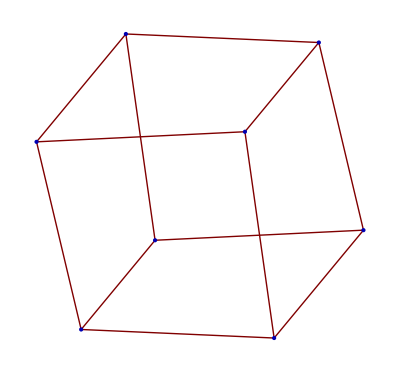
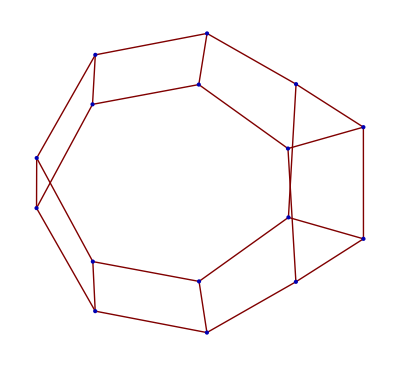
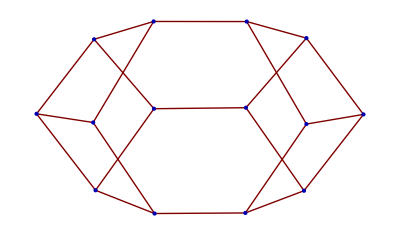
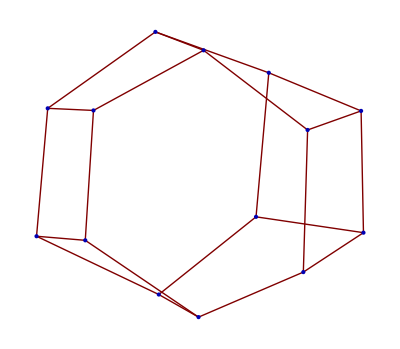
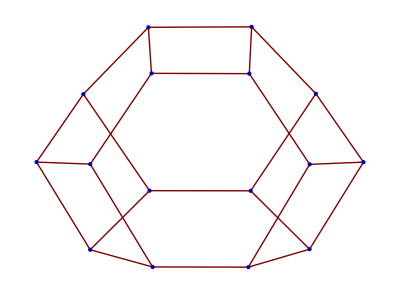
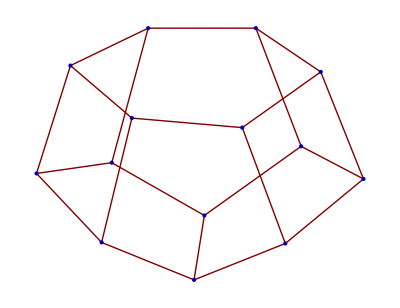
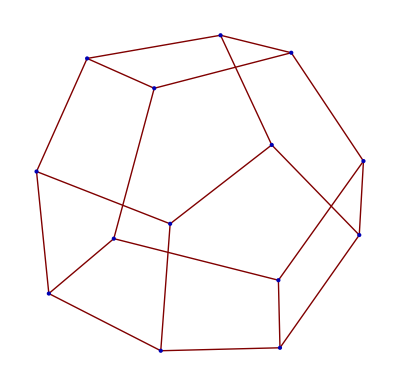
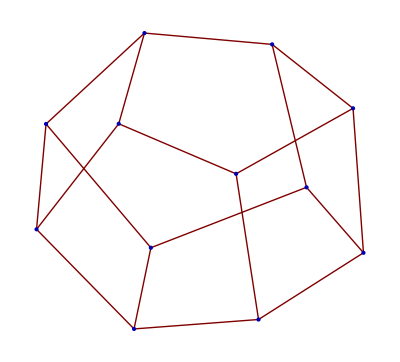
{Cube→-Graphics-,p4444445577→-Graphics-,p444444666→-Graphics-,p444445566→-Graphics-,p4444455666→-Graphics-,p444455556→-Graphics-,p444555555→-Graphics-,p55554444→-Graphics-,pAAAA→-Graphics-,pAAAB→-Graphics-,pAAAC→-Graphics-,pAAAD→-Graphics-,pAAAE→-Graphics-,pAAAF→-Graphics-,pAAAG→-Graphics-,pAAAH→-Graphics-,pAAAI→-Graphics-,Prism[5]→-Graphics-,Prism[6]→-Graphics-,Prism[7]→-Graphics-,Prism[8]→-Graphics-,Prism[9]→-Graphics-}

```mathematica
DisplayPolyhedraNames[]
```

```mathematica
PolyhedraNames=Drop[PolyhedraNames,-4];
```